```mathematica
alphaRod = 0.4;
alphaSheet = 0.02;
epsilon = 0.1;
diffConst[x_]:=Piecewise[{{alphaSheet, x < 0.5-epsilon},{alphaRod,x ≥ 0.5-epsilon && x < 0.5 + epsilon},{alphaSheet,x≥0.5+epsilon}}];
initFnoEscape[x_]:= 20*x^2*(x-1)^2; initFwithEscape[x_]:= -20*x*(x-1);
```

```mathematica
(*These are the unit square systems with and without the rod where no heat escapes*)
systemWithRod = NDSolveValue[{D[u[x,t],t]-diffConst[x]*Laplacian[u[x,t],{x}]==0,DirichletCondition[u[x,t]==initFnoEscape[x],t==0]},u,{x,0,1},{t,0,10}];
systemNoRod = NDSolveValue[{D[u[x,t],t]-alphaSheet*Laplacian[u[x,t],{x}]==0,DirichletCondition[u[x,t]==initFnoEscape[x],t==0]},u,{x,0,1},{t,0,10}];
(*These are the unit square systems where the end temp is constant so a lot of heat escapes*)
systemWithRodEscape = NDSolveValue[{D[u[x,t],t]-diffConst[x]*Laplacian[u[x,t],{x}]==0,DirichletCondition[u[x,t]==initFwithEscape[x],t==0],DirichletCondition[u[x,t]==0,x==0||x==1]},u,{x,0,1},{t,0,10}];
systemNoRodEscape = NDSolveValue[{D[u[x,t],t]-alphaSheet*Laplacian[u[x,t],{x}]==0,DirichletCondition[u[x,t]==initFwithEscape[x],t==0],DirichletCondition[u[x,t]==0,x==0||x==1]},u,{x,0,1},{t,0,10}];
```

NDSolveValue::femcscd: The PDE is convection dominated and the result may not be stable. Adding artificial diffusion may help.

```mathematica
(*Shows the total energy in systems*)
energyRodSys[t_]:=Integrate[systemNoRod[x,t],{x,0,1}];
energyNoRodSys[t_]:=Integrate[systemWithRod[x,t],{x,0,1}];
energyRodSysEscape[t_]:=Integrate[systemNoRodEscape[x,t],{x,0,1}];
energyNoRodSysEscape[t_]:=Integrate[systemWithRodEscape[x,t],{x,0,1}];
```

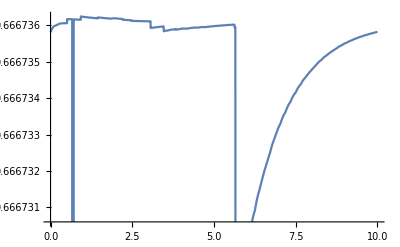

```mathematica
Plot[energyRodSys[t],{t,0,10}]
```

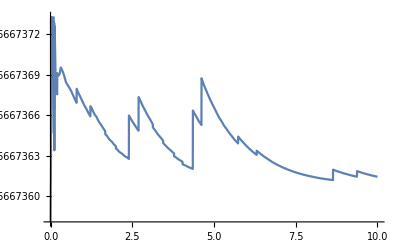

```mathematica
Plot[energyNoRodSys[t],{t,0,10}]
```

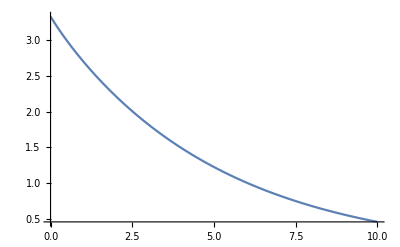

```mathematica
Plot[energyRodSysEscape[t],{t,0,10}]
```

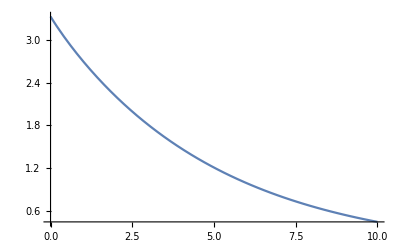

```mathematica
Plot[energyNoRodSysEscape[t],{t,0,10}]
```

```mathematica
(* Temperature Flow Graphs*)
tempFlowRodSys[x_,t_]:=D[systemWithRod[xx,tt],xx]/.{xx->x,tt->t};
tempFlowNoRodSys[x_,t_]:=D[systemNoRod[xx,tt],xx]/.{xx->x,tt->t};
tempFlowRodSysEscape[x_,t_]:=D[systemWithRodEscape[xx,tt],xx]/.{xx->x,tt->t};
tempFlowNoRodSysEscape[x_,t_]:=D[systemNoRodEscape[xx,tt],xx]/.{xx->x,tt->t};
```

```mathematica
(*Shows the temp flow in system without rod*)
Manipulate[Plot[{tempFlowNoRodSys[x,t],4,-4},{x,0,1}],{t,0,10}]
```

```mathematica
(*Shows temp flow in system with rod*)
Manipulate[Plot[{tempFlowRodSys[x,t],4,-4},{x,0,1}],{t,0,10}]
```

```mathematica
(*Temp flow in system without rod where temp escapes out the ends*)
Manipulate[Plot[{tempFlowNoRodSysEscape[x,t],20,-20},{x,0,1}],{t,0,10}]
```

```mathematica
(*Temp flow in system with rod where temp escapes out the ends*)
Manipulate[Plot[{tempFlowRodSysEscape[x,t],20,-20},{x,0,1}],{t,0,10}]
```